```mathematica
2-2
```

# Physicist's Introduction to Mathematica 7

## Fourth Edition 2007

## PHYSICS 200

Nicholas Wheeler

REED COLLEGE

## Laboratory 4

## Obtaining/Displaying Solutions of Ordinary Differential Equations

Many problems in physics—as also elsewhere in the pure/applied mathematics of the last three centuries—assume this form: Find the x(t) which, in collaboration with its derivatives, satisfies an equation of the form

```mathematica
F[x[t],x'[t],x''[t],...]==0
```

together with prescribed initial/boundary conditions. Newton's 2nd Law provides the classic case in point: it presents the problem of dynamical motion as the problem of solving

```mathematica
m x''[t]==F[x[t]]
Initial conditions: x[Subscript[t, 0]]==Subscript[x, 0]  and   x'[Subscript[t, 0]]==Subscript[v, 0]
```

or, more generally, of solving

m x''[t]==F_x[x[t],y[y],z[t]]
m y''[t]==F_y[x[t],y[y],z[t]]
m z''[t]==F_z[x[t],y[y],z[t]]
Six initial conditions required

which comprise a coupled system of 2nd order ODEs.

REMARK: Such equations are called ordinary differential equations (ODEs) because the unknown functions are functions of a single independent variable, so only ordinary derivatives are encountered. "Fields" are functions of several independent variables; in field theory one therefore encounters partial derivatives, and is led to the theory of partial differential equations (PDEs) … which traditionally has been thought of as a different subject altogether (and much more difficult), but which Mathematica equips one to approach—numerically, if not analytically—with almost equal ease.

The ODE literature presents a bewildering collection of tricks devised by generations of mathematicians to solve ODEs of this or that specialized type. Most of those tricks pertain exclusively to ODEs that can be solved in terms of named functions (many "named functions" arose from the theory of ODEs). But many/most of the ODEs encountered in realistic physical situations elude the network of known tricks: such equations must be solved numerically. The situation is further complicated by the circumstance that it is difficult, even with a virtuoso command of the tricks, to know in advance whether or not the particular ODE in hand can be brought to such a form that it yields to some trick. Today all is changed, simplified, because…

• Mathematica knows all the tricks.

• Mathematica permits a simple, unified approach to the solution of ODEs.

The commands

```mathematica
?DSolve
?NDSolve
```

DSolve[eqn,y,x] solves a differential equation for the function y, with independent variable x. 
DSolve[{eqn_1,eqn_2,…},{y_1,y_2,…},x] solves a list of differential equations. 
DSolve[eqn,y,{x_1,x_2,…}] solves a partial differential equation.

NDSolve[eqns,y,{x,x_min,x_max}] finds a numerical solution to the ordinary differential equations eqns for the function y with the independent variable x in the range x_min to x_max. 
NDSolve[eqns,y,{x,x_min,x_max},{t,t_min,t_max}] finds a numerical solution to the partial differential equations eqns. 
NDSolve[eqns,{y_1,y_2,…},{x,x_min,x_max}] finds numerical solutions for the functions y_i.

lead (follow the »s) to discussion of the commands most fundamental to this field. In the necessarily brief discussion that follows I will let physical problems provide my motivation.

### Exponential Population Growth

Let P[t] describe the size of a population at time t .  Population growth can, in the simplest model, be described

P'[t]==a P[t]

The general solution is obvious, but let us ask Mathematica to do the work:

```mathematica
DSolve[P'[t]==a P[t],P[t],t]
```

{{P[t]→ⅇ^(a t) C[1]}}

The output is a replacement list (in this case, a one-element list, buried within a list).  C[1] is the name Mathematica gives to the arbitrary constant of integration.

NOTE: The general solution of an ODE (or system of ODEs) is expected to contain constants of integration equal in number to the order of the ODE (or system). The present system is of first order, so we encounter only a solitary constant.

We could, at this point, reach inside the nested braces and by hand extract the information we seek, writing (say)

```mathematica
solution=ⅇ^(a t) C[1]
```

ⅇ^(a t) C[1]

and verifying that indeed

```mathematica
D[solution, t]==a*solution
```

True

But, in more complicated situations, "by-hand extraction"—though recommended by its straightforward simplicity—can become a bit tedious. To illustrate the point, look to the solution of a coupled pair of first-order ODEs (system of second order: note the appearance of both C[1] and C[2] in the output):

```mathematica
DSolve[{p'[t]==a q[t],q'[t]==b p[t]}, {p[t],q[t]}, t]
```

{{p[t]→1/2 ⅇ^(-√a √b t) (1+ⅇ^(2 √a √b t)) C[1]+(√a ⅇ^(-√a √b t) (-1+ⅇ^(2 √a √b t)) C[2])/(2 √b),q[t]→(√b ⅇ^(-√a √b t) (-1+ⅇ^(2 √a √b t)) C[1])/(2 √a)+1/2 ⅇ^(-√a √b t) (1+ⅇ^(2 √a √b t)) C[2]}}

"By hand" we reach inside the braces {{ }} and extract the functions

```mathematica
psol=1/2 ⅇ^(-√a √b t) (1+ⅇ^(2 √a √b t)) C[1]+(√a ⅇ^(-√a √b t) (-1+ⅇ^(2 √a √b t)) C[2])/(2 √b);
qsol=(√b ⅇ^(-√a √b t) (-1+ⅇ^(2 √a √b t)) C[1])/(2 √a)+1/2 ⅇ^(-√a √b t) (1+ⅇ^(2 √a √b t)) C[2];
```

which we verify do indeed comprise solutions of the coupled system:

```mathematica
{D[psol,t]==a qsol,
D[qsol,t]==b psol}//Simplify
```

{True,True}

#### A Short Digression—Stan Wagon's Extraction Trick

Stan Wagon describes (on 295 of his Mathematica in Action (2^nd edition 1999)) a better procedure, that makes use of the ReplaceAll and First commands. ReplaceAll (denoted /.) we have already encountered, and works like this:

```mathematica
1+x^2/.x->tom
{a,b,x,1/(1+x),c}/.x-> dick
```

1+tom^2

{a,b,dick,1/(1+dick),c}

First is equivalent to the post-command ⟦1⟧; both act to pluck the first element from a list:

```mathematica
First[{tom, dick, harry}]
{tom, dick, harry}⟦1⟧
{tom, dick, harry}⟦2⟧
```

tom

tom

dick

Returning now to our first example, to reproduce the solution we have extracted by hand Stan Wagon presents

```mathematica
HisSolution=P[t]/.First[DSolve[P'[t]==a P[t],P[t],t]]
```

ⅇ^(a t) C[1]

In the second example he would have us write

```mathematica
{HisPsol,HisQsol}={p[t],q[t]}/.First[DSolve[{p'[t]==a q[t],q'[t]==b p[t]}, {p[t],q[t]}, t]]
```

{1/2 ⅇ^(-√a √b t) (1+ⅇ^(2 √a √b t)) C[1]+(√a ⅇ^(-√a √b t) (-1+ⅇ^(2 √a √b t)) C[2])/(2 √b),(√b ⅇ^(-√a √b t) (-1+ⅇ^(2 √a √b t)) C[1])/(2 √a)+1/2 ⅇ^(-√a √b t) (1+ⅇ^(2 √a √b t)) C[2]}

which (it is now not quite obvious) does indeed reproduce our own results:

```mathematica
{HisPsol, HisQsol}=={psol,qsol}
```

True

#### Exponential Population Growth Resumed: the Slope Field Concept

The equation

```mathematica
y'[x]==f[x,y]
```

tells us that y[x] describes a curve with the property that when it passes through the point (x,y) has slope f[x,y].  If we planted unit vectors with the prescribed slopes on the (x,y)-plane we could obtain y[x] by simply "threading through" that field of vectors.  I illustrate the idea as it relates to the exponential growth model

```mathematica
P'[t]==P[t]
```

The critical resouce here is the command VectorFieldPlot, access to which is provided by a standard package which we now import:

```mathematica
Needs["VectorFieldPlots`"]
```

General::obspkg: VectorFieldPlots` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
?VectorFieldPlot
```

VectorFieldPlot [ {f_x,f_y}, { x ,x_min,x_max}, { y ,y_min,y_max}] generates a plot of the vector field given by the vector valued function  {f_x,f_y} as a function of  x  and  y .
 VectorFieldPlot [ {f_x,f_y}, { x ,x_min,x_max, dx }, { y ,y_min,y_max, dy }] uses steps  dx  in variable  x , and steps  dy  in variable  y .

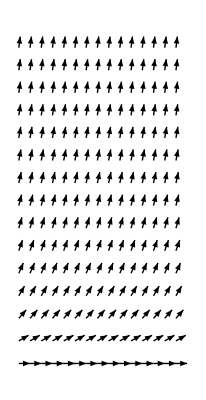

```mathematica
Slopefield=VectorFieldPlot[{1/(√(1+P^2)),P/(√(1+P^2))},{t,-2,2},{P,0,8},AspectRatio->Automatic]
```

The  general solution of our exponential growth equation is

```mathematica
P[t_,k_]:=k ⅇ^-t
```

of which we plot a particular solution:

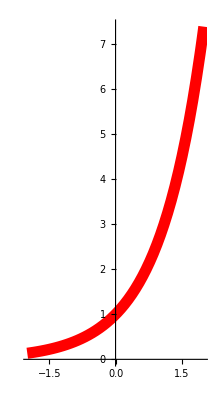

```mathematica
ParticularSolution=Plot[ⅇ^t,{t,-2,2},AspectRatio->Automatic,PlotStyle->{Red,Thickness[0.02]}]
```

Superimposing the figures

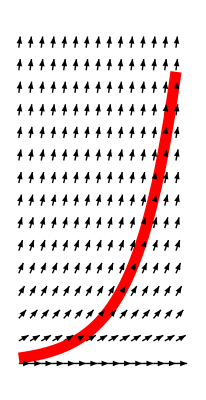

```mathematica
Show[Slopefield,ParticularSolution]
```

makes vividly evident how the red solution "threads through" the slope field, and it becomes obvious what the solution that passes through any specified point would look like.

Variants of the idea just illustrated are of very widespread utility, and often help one to grasp the qualitative essentials of complex situations.

### Limited Growth: The "Logistic Model"

Modify the right side of the preceding ODE so as to have

```mathematica
P'[t]==P[t](5-P[t])
P[0]=1
```

From

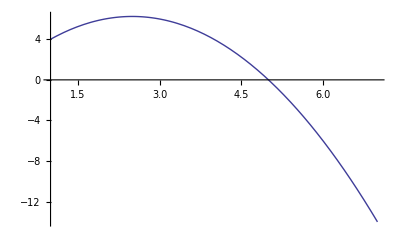

```mathematica
Plot[P(5-P),{P,1,7}]
```

we see that the population grows if P < 5, holds steady at P = 5, diminishes if P > 5. Proceeding

```mathematica
logistic=p'[t]-p[t](5-p[t]);
```

```mathematica
p[t]/.First[DSolve[{logistic==0,p[0]==1},p[t],t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(5 ⅇ^(5 t))/(4+ⅇ^(5 t))

we obtain the particular population curve in which we have declared an interest. We plot it:

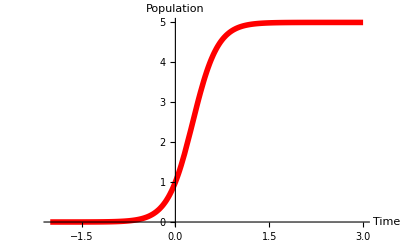

```mathematica
LogisticPopulationPlot=Plot[(5 ⅇ^(5 t))/(4+ⅇ^(5 t)),{t,-2,3},
PlotRange->All,PlotStyle->{Red,Thickness[0.01]},AxesLabel->{Time, Population}]
```

Next, we plot the associated slope field

VectorFieldPlot[{1/(√(1+(p(5-p))^2)),(p(5-p))/(√(1+(p(5-p))^2))},{t,-2,3},{p,0,6},AspectRatio→Automatic]

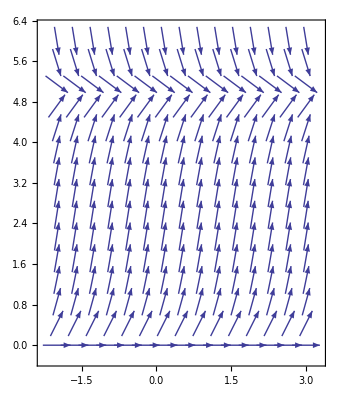

```mathematica
VectorPlot[{1/(√(1+(p(5-p))^2)),(p(5-p))/(√(1+(p(5-p))^2))},{t,-2,3},{p,0,6},AspectRatio->Automatic]
```

and superimpose our particular solution on that slope field:

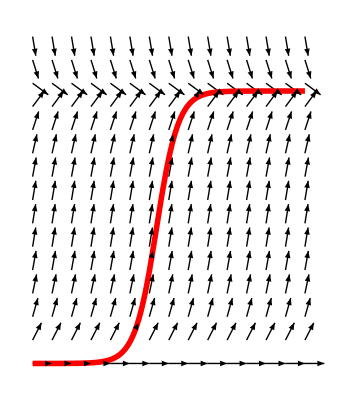

```mathematica
Show[LogisticSlopefield,LogisticPopulationPlot]
```

### Harmonic Oscillator

The equation of physical interest reads

```mathematica
m x''[t]=-m ω^2 x[t]
```

and in the typical special case to which I will restrict my attention (set the m = 1 and set  ω  = 3) assumes the form

```mathematica
x''[t]=-3^2 x[t]
```

We declare an interest in motion that arises from the initial conditions

```mathematica
x[0]=0
x'[t]=1
```

It is from Abell & Braselton (Differential Equations with Mathematica (1997), page 240) that I have borrowed the commands that (after the adjustments required by Mathematica 6) produce the following diagram of a mass attached to a spring:

REMARK: There is much of vaue to be learned from the following commands (concerning which Abell & Braselton supply explanatory remarks), but today is not the day…and soon the logic of the commands  will anyway be clear to you.

```mathematica
zigzag[{a_,b_},{c_,d_},n_,ϵ_]:=Module[{length, points, pairs},
length=d-b;
points=Table[b+(i length)/n,{i,1,n-1}];
pairs=Table[{a+ϵ(-1)^i, points⟦i⟧},{i,1,n-1}];
PrependTo[pairs,{a,b}];AppendTo[pairs, {c,d}];
Line[pairs]]
```

```mathematica
typicalposition=3/4;
```

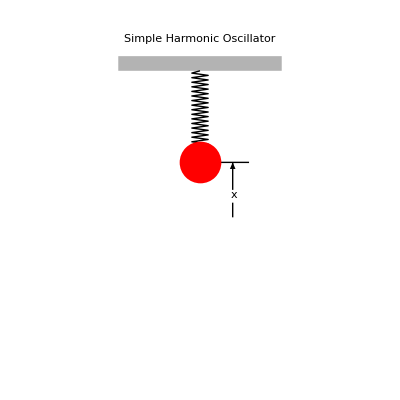

```mathematica
Show[Graphics[
{zigzag[{0,typicalposition}, {0,2},40,.05],
PointSize[.075],
{Red,Point[{0,typicalposition}]},
Line[{{.1,.75},{.3,.75}}],
Line[{{.2,0},{.2,.2}}],
Arrowheads[.03],
Arrow[{{.2,.375},{.2,.75}}],
Text["x",{.205,.3}],
{GrayLevel[.7],Rectangle[{-.5,2},{.5,2.2}]}}],
PlotLabel->StyleForm["Simple Harmonic Oscillator",
FontFamily->"Times-Bold",
FontSize->16],
Axes->Automatic,
AxesStyle->GrayLevel[.5],
Ticks->None,
PlotRange->{{-1,1},{-2,2.2}},
AspectRatio->1]
```

We ask Mathematica to solve the equation of motion (which is an ODE of now second order), subject to the prescribed initial conditions:

```mathematica
OscillatorMotion=x[t]/.First[DSolve[{x''[t]==-3^2 x[t],x[0]==0,x'[0]==3},x[t],t]]
```

Sin[3 t]

```mathematica
OscillatorMotion
```

Sin[3 t]

```mathematica
f[t_]:=OscillatorMotion
```

```mathematica
f[t]
```

Sin[3 t]

There are several ways to display that information; the most obvious is to simply plot it

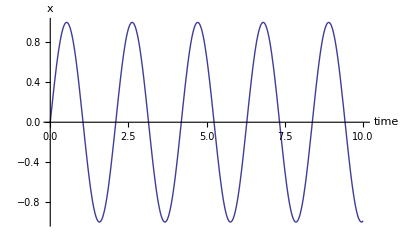

```mathematica
Plot[OscillatorMotion, {t,0,10}, AxesLabel->{"time","x"}]
```

Or we might animate the preceding diagram:

```mathematica
OscillatorMovie[t_]:=Show[Graphics[
{zigzag[{0,Sin[3t]}, {0,2},40,.05],
PointSize[.075],
{Red,Point[{0,Sin[3t]}]},
{GrayLevel[.7],Rectangle[{-.5,2},{.5,2.2}]}}],
PlotLabel->StyleForm["Animated Simple Harmonic Oscillator",
FontFamily->"Times-Bold",
FontSize->16],
Axes->Automatic,
AxesStyle->GrayLevel[.5],
Ticks->None,
PlotRange->{{-1,1},{-2,2.2}},
AspectRatio->1]
```

```mathematica
Animate[OscillatorMovie[t],{t,0,2π/3}, AnimationRunning->False]
```

### Damped Harmonic Oscillator

The standard model of a damped oscillator can be described

```mathematica
m x''[t]=-2m b x'[t]-m ω^2 x[t]
```

where b is the "damping coefficient." Looking to the general solution (with some not-quite-general initial conditions)

```mathematica
DampedOscillatorMotion=x[t]/.First[DSolve[{x''[t]==-2b x'[t]-ω^2 x[t],x[0]==0,x'[0]==v},x[t],t]]
```

-((ⅇ^(t (-b-√(b^2-ω^2)))-ⅇ^(t (-b+√(b^2-ω^2)))) v)/(2 √(b^2-ω^2))

we see that cases with strong damping (b^2>ω^2) are qualitatively distinct from those with weak damping (b^2<ω^2), and that the critical case b^2=ω^2 separates the two regimes. To illustrate the point, we (simply to reduce the number of free variables) set ω = v = 3 and look serially to typical instances of each of those characteristic types of damped oscillator motion:

#### Underdamped Case

We look to the case b^2=1/4≪ ω^2. While we could specialize/simplify the general result already in hand

```mathematica
ExpToTrig[((ⅇ^(t (-b-√(b^2-ω^2)))-ⅇ^(t (-b+√(b^2-ω^2)))) v)/(2 √(b^2-ω^2))/.{b->1/2, ω->3,v->3}]//Simplify
```

-(6 Sin[(√35 t)/2] (Cosh[t/2]-Sinh[t/2]))/(√35)

```mathematica
TrigToExp[Cosh[t/2]-Sinh[t/2]]
```

ⅇ^(-t/2)

it is simpler to back up and solve the particularized differential equation:

```mathematica
UnderdampedOscillation=x[t]/.First[DSolve[{x''[t]==-2(1/2) x'[t]-3^2 x[t],x[0]==0,x'[0]==3},x[t],t]]
```

(6 ⅇ^(-t/2) Sin[(√35 t)/2])/(√35)

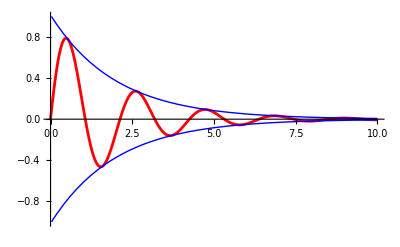

```mathematica
Plot[{(6 ⅇ^(-t/2) Sin[(√35 t)/2])/(√35),(6 ⅇ^(-t/2))/(√35),-(6 ⅇ^(-t/2))/(√35)},{t,0,10},PlotStyle->{{Red, Thickness[.005]},Blue,Blue},
PlotRange->{-1,1}]
```

#### Overdamped Case

We look to the case b^2=4^2> ω^2.

```mathematica
OverdampedOscillation=x[t]/.First[DSolve[{x''[t]==-2(4) x'[t]-3^2 x[t],x[0]==0,x'[0]==3},x[t],t]]
```

-(3 (ⅇ^((-4-√7) t)-ⅇ^((-4+√7) t)))/(2 √7)

This expression is assembled from exponentials that die at two different rates, on fast, the other slow:

```mathematica
N[{(-4-√7),(-4+√7)}]
```

{-6.64575,-1.35425}

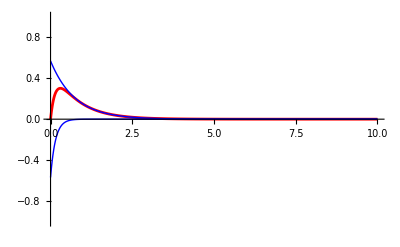

```mathematica
Plot[{-(3 (ⅇ^((-4-√7) t)-ⅇ^((-4+√7) t)))/(2 √7),-(3 (ⅇ^((-4-√7) t)))/(2 √7),-(3 (-ⅇ^((-4+√7) t)))/(2 √7)},{t,0,10},PlotStyle->{{Red, Thickness[.005]},Blue,Blue},
PlotRange->{-1,1}]
```

#### Critically Damped Case

We look finally to the case b^2=3^2= ω^2.

```mathematica
CriticallyDampedOscillation=x[t]/.First[DSolve[{x''[t]==-2(3) x'[t]-3^2 x[t],x[0]==0,x'[0]==3},x[t],t]]
```

3 ⅇ^(-3 t) t

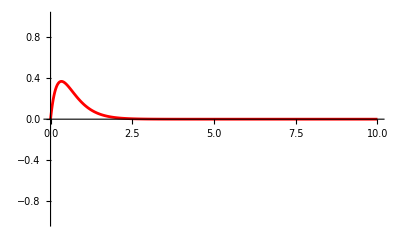

```mathematica
Plot[3 ⅇ^(-3 t) t,{t,0,10},PlotStyle->{Red, Thickness[.005]},
PlotRange->{-1,1}]
```

Damping in the critical case is not exponential, but is quicker than in all other cases, whether overdamped (compare this figure with the preceding one) or underdamped.

#### Underdamped Display with Adjustable Damping Coefficient

It is evident that the solution

```mathematica
DampedOscillatorMotion=x[t]/.First[DSolve[{x''[t]==-2b x'[t]-3^2 x[t],x[0]==0,x'[0]==3},x[t],t]]
```

-(3 (ⅇ^((-b-√(-9+b^2)) t)-ⅇ^((-b+√(-9+b^2)) t)))/(2 √(-9+b^2))

can in the underdamped case be written

```mathematica
3(ϵ^(-b t)Sin[√(9-b^2)t])/(√(9-b^2))
```

The following figure shows how damped oscillation responds when the damping coefficient slides up to a value just shy of the critical value. Note the method used to set the default value damping coefficient equal to the value used to construct the previous underdamped figure:  b = 1/4.

```mathematica
Manipulate[Plot[{3(ⅇ^(-b t)Sin[√(9-b^2)t])/(√(9-b^2)),3 ⅇ^(-b t)/(√(9-b^2)),-3 ⅇ^(-b t)/(√(9-b^2))},{t,0,10}, PlotRange->{-1,1},PlotStyle->{{Red, Thickness[.005]},{Blue},{Blue}}],{{b,1/4},0,2.9}]
```

INSTRUCTIONS: Press the "+ button" at the right end of the slider to expose the control buttons and indicator.

## Phase Space Methods

Any 2nd-order equation of motion (describing motion of a particle in one-dimensional space) can be converted into a pair of 1st-order equations which describe the motion of an abstract point in two-dimensional "phase space," and that is for many purposes often the most powerfully informative way to proceed. We touch here on the idea that lies at the heart of Hamiltonian mechanics, which we now illustrate as it pertains to damped oscillators.

The damped oscillator equation

m x''[t]=-2m b x'[t]-m ω^2 x[t]

is readily recovered from the following pair of 1st-order equations:

```mathematica
x'[t]==p[t]/m
p'[t]==-2b p[t]-m ω^2 x[t]
```

If we particularize as before, setting m = 1 and ω = 3, we have

```mathematica
x'[t]==p[t]
p'[t]==-2b p[t]-3^2 x[t]
```

Look to the motion that results when (as before) we set

```mathematica
b=1/2
x[0]=0
p[0]=3
```

```mathematica
{DampedPosition, DampedMomentum}={x[t],p[t]}/.First[DSolve[{x'[t]==p[t],p'[t]==-2 1/2 x'[t]-3^2 x[t],x[0]==0,p[0]==3},{x[t],p[t]},t]]
```

{(6 ⅇ^(-t/2) Sin[(√35 t)/2])/(√35),3/35 ⅇ^(-t/2) (35 Cos[(√35 t)/2]-√35 Sin[(√35 t)/2])}

```mathematica
dampedposition[t_]:=(6 ⅇ^(-t/2) Sin[(√35 t)/2])/(√35)
dampedmomentum[t_]:=3/35 ⅇ^(-t/2) (35 Cos[(√35 t)/2]-√35 Sin[(√35 t)/2])
```

For comparative purposes, we turn off the damping (set b = 0) and get

```mathematica
{UndampedPosition,UndampedMomentum}={x[t],p[t]}/.First[DSolve[{x'[t]==p[t],p'[t]==-3^2 x[t],x[0]==0,p[0]==3},{x[t],p[t]},t]]
```

{Sin[3 t],3 Cos[3 t]}

```mathematica
undampedposition[t_]:=UndampedPosition
undampedmomentum[t_]:=UndampedMomentum
```

dampedposition[t_] := DampedPosition
dampedmomentum[t_] := DampedMomentum

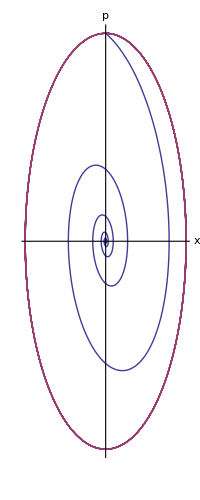

```mathematica
ComparativePhaseTrajectories=ParametricPlot[{{dampedposition[t],dampedmomentum[t]},{undampedposition[t],undampedmomentum[t]}},{t,0,10},
AxesLabel->{"x","p"},
Ticks->None,
PlotRange->All,
AspectRatio->Automatic]
```

In the absence of damping, the moving phase point traces a "constant-energy ellipse." In the presence of damping, energy loss causes it to spiral inward to extinction. Here is an animated representation of the damped motion:

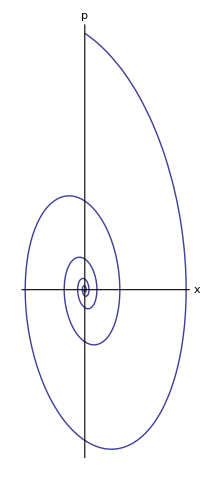

```mathematica
Curve=ParametricPlot[{dampedposition[t],dampedmomentum[t]},{t,0,10},
AxesLabel->{"x","p"},
Ticks->None,
PlotRange->All,
AspectRatio->Automatic]
```

```mathematica
dampedposition[t]
dampedmomentum[t]
```

(6 ⅇ^(-t/2) Sin[(√35 t)/2])/(√35)

3/35 ⅇ^(-t/2) (35 Cos[(√35 t)/2]-√35 Sin[(√35 t)/2])

```mathematica
movingdampedstatepoint[t_]:=Graphics[{PointSize[.07],
Red,
Point[{dampedposition[t], dampedmomentum[t]}]}];
```

```mathematica
Animate[Show[{Curve,movingdampedstatepoint[t]}],{t,0,10,.005},AnimationRunning->False]
```

INSTRUCTIONS: Hit the Play button to see the movie. You get better resolution—particularly in opening scene—if you use the slider to advance the film.

Looking specifically to the energetics of the motion—i.e., to

```mathematica
energy=m(velocity)^2/2+m ω^2(displacement)^2/2
```

—we proceed as follows:

```mathematica
dampedenergy[t_]:=dampedmomentum[t]^2/2+(3^2 dampedposition[t]^2)/2
undampedenergy[t_]:=undampedmomentum[t]^2/2+(3^2 undampedposition[t]^2)/2
```

```mathematica
dampedenergy[t]//Simplify
undampedenergy[t]//Simplify
```

-9/70 ⅇ^-t (-36+Cos[√35 t]+√35 Sin[√35 t])

9/2

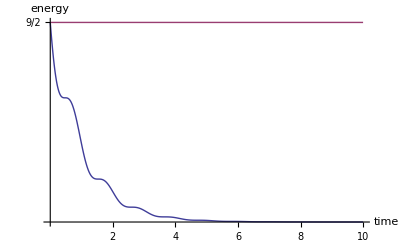

```mathematica
Plot[{dampedenergy[t],undampedenergy[t]}, {t,0,10}, Ticks->{{2,4,6,8,10},{9/2}},AxesLabel->{"time","energy"}]
```

### Harmonically Forced Damped Oscillator

In the absence of damping (and also of forcing) we had

```mathematica
x[t]/.First[DSolve[{x''[t]+3^2 x[t]==0,x[0]==0,x'[0]==3},x[t],t]]
```

Sin[3 t]

```mathematica
UnforcedUndampedPeriod=(2π)/3//N
```

2.0944

In the presence of weak damping (still no forcing) the adjusted motion became

```mathematica
x[t]/.First[DSolve[{x''[t]+x'[t]+3^2 x[t]==0,x[0]==0,x'[0]==3},x[t],t]]
```

(6 ⅇ^(-t/2) Sin[(√35 t)/2])/(√35)

Since the motion is has become non-periodic, the "period" concept is replaced by "time between zero crossings," and it is in that sense that we have

```mathematica
UnforcedDampedPeriod=(2π)/((√35)/2)//N
```

2.1241

which is slightly prolonged, as is evident in the following figure:

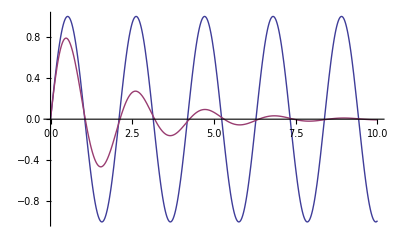

```mathematica
Plot[{Sin[3 t],(6 ⅇ^(-t/2) Sin[(√35 t)/2])/(√35)},{t,0,10}]
```

Now we turn on a harmonic

```mathematica
ForcingFunction[t_]:= Sin[2t]
```

with

```mathematica
ForcingPeriod=(2π)/2//N
```

3.14159

The equation of motion now gives (this will take a minute)

```mathematica
x[t]/.First[DSolve[{x''[t]+x'[t]+3^2 x[t]==Sin[2t],x[0]==0,x'[0]==3},x[t],t]]
```

(ⅇ^(-t/2) (-140 Cos[(√35 t)/2]+70 ⅇ^(t/2) Cos[(√35 t)/2] Cos[1/2 (-4+√35) t]+13 √35 ⅇ^(t/2) Cos[(√35 t)/2] Cos[1/2 (-4+√35) t]+70 ⅇ^(t/2) Cos[(√35 t)/2] Cos[1/2 (4+√35) t]-13 √35 ⅇ^(t/2) Cos[(√35 t)/2] Cos[1/2 (4+√35) t]-312 √35 Sin[(√35 t)/2]-175 ⅇ^(t/2) Cos[1/2 (-4+√35) t] Sin[(√35 t)/2]-18 √35 ⅇ^(t/2) Cos[1/2 (-4+√35) t] Sin[(√35 t)/2]+175 ⅇ^(t/2) Cos[1/2 (4+√35) t] Sin[(√35 t)/2]-18 √35 ⅇ^(t/2) Cos[1/2 (4+√35) t] Sin[(√35 t)/2]+175 ⅇ^(t/2) Cos[(√35 t)/2] Sin[1/2 (-4+√35) t]+18 √35 ⅇ^(t/2) Cos[(√35 t)/2] Sin[1/2 (-4+√35) t]-175 ⅇ^(t/2) Cos[(√35 t)/2] Sin[1/2 (4+√35) t]+18 √35 ⅇ^(t/2) Cos[(√35 t)/2] Sin[1/2 (4+√35) t]+70 ⅇ^(t/2) Sin[(√35 t)/2] Sin[1/2 (4+√35) t]-13 √35 ⅇ^(t/2) Sin[(√35 t)/2] Sin[1/2 (4+√35) t]-70 ⅇ^(t/2) Sin[(√35 t)/2] Sin[2 t-(√35 t)/2]-13 √35 ⅇ^(t/2) Sin[(√35 t)/2] Sin[2 t-(√35 t)/2]))/(70 (-13+2 √35) (13+2 √35))

```mathematica
Simplify[%]
```

(-70 Cos[2 t]+70 ⅇ^(-t/2) Cos[(√35 t)/2]+175 Sin[2 t]+156 √35 ⅇ^(-t/2) Sin[(√35 t)/2])/1015

```mathematica
ForcedDampedMotion[t_]:=(-70 Cos[2 t]+70 ⅇ^(-t/2) Cos[(√35 t)/2]+175 Sin[2 t]+156 √35 ⅇ^(-t/2) Sin[(√35 t)/2])/1015
```

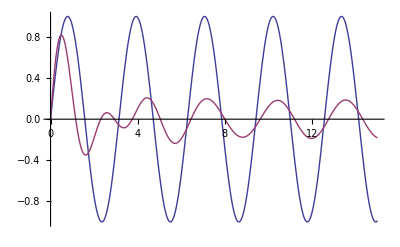

```mathematica
Plot[{ForcingFunction[t],ForcedDampedMotion[t]},{t,0,15}]
```

We see that, after initial transcients have damped out, the motion acquires the frequency/period of the forcing function, but is shifted in phase.

Let us suppose now that the angular frequency is adjustable (call it Ω):

```mathematica
x[t]/.First[DSolve[{x''[t]+x'[t]+3^2 x[t]==Sin[Ω t],x[0]==0,x'[0]==3},x[t],t]]
```

-(ⅇ^(-t/2) (70 Ω Cos[(√35 t)/2]-9 √35 ⅇ^(t/2) Cos[(√35 t)/2] Cos[1/2 t (√35-2 Ω)]-35 ⅇ^(t/2) Ω Cos[(√35 t)/2] Cos[1/2 t (√35-2 Ω)]-√35 ⅇ^(t/2) Ω^2 Cos[(√35 t)/2] Cos[1/2 t (√35-2 Ω)]+9 √35 ⅇ^(t/2) Cos[(√35 t)/2] Cos[1/2 t (√35+2 Ω)]-35 ⅇ^(t/2) Ω Cos[(√35 t)/2] Cos[1/2 t (√35+2 Ω)]+√35 ⅇ^(t/2) Ω^2 Cos[(√35 t)/2] Cos[1/2 t (√35+2 Ω)]+972 √35 Sin[(√35 t)/2]-34 √35 Ω Sin[(√35 t)/2]-204 √35 Ω^2 Sin[(√35 t)/2]+4 √35 Ω^3 Sin[(√35 t)/2]+12 √35 Ω^4 Sin[(√35 t)/2]+315 ⅇ^(t/2) Cos[1/2 t (√35-2 Ω)] Sin[(√35 t)/2]+17 √35 ⅇ^(t/2) Ω Cos[1/2 t (√35-2 Ω)] Sin[(√35 t)/2]-35 ⅇ^(t/2) Ω^2 Cos[1/2 t (√35-2 Ω)] Sin[(√35 t)/2]-2 √35 ⅇ^(t/2) Ω^3 Cos[1/2 t (√35-2 Ω)] Sin[(√35 t)/2]-315 ⅇ^(t/2) Cos[1/2 t (√35+2 Ω)] Sin[(√35 t)/2]+17 √35 ⅇ^(t/2) Ω Cos[1/2 t (√35+2 Ω)] Sin[(√35 t)/2]+35 ⅇ^(t/2) Ω^2 Cos[1/2 t (√35+2 Ω)] Sin[(√35 t)/2]-2 √35 ⅇ^(t/2) Ω^3 Cos[1/2 t (√35+2 Ω)] Sin[(√35 t)/2]-315 ⅇ^(t/2) Cos[(√35 t)/2] Sin[1/2 t (√35-2 Ω)]-17 √35 ⅇ^(t/2) Ω Cos[(√35 t)/2] Sin[1/2 t (√35-2 Ω)]+35 ⅇ^(t/2) Ω^2 Cos[(√35 t)/2] Sin[1/2 t (√35-2 Ω)]+2 √35 ⅇ^(t/2) Ω^3 Cos[(√35 t)/2] Sin[1/2 t (√35-2 Ω)]-9 √35 ⅇ^(t/2) Sin[(√35 t)/2] Sin[1/2 t (√35-2 Ω)]-35 ⅇ^(t/2) Ω Sin[(√35 t)/2] Sin[1/2 t (√35-2 Ω)]-√35 ⅇ^(t/2) Ω^2 Sin[(√35 t)/2] Sin[1/2 t (√35-2 Ω)]+315 ⅇ^(t/2) Cos[(√35 t)/2] Sin[1/2 t (√35+2 Ω)]-17 √35 ⅇ^(t/2) Ω Cos[(√35 t)/2] Sin[1/2 t (√35+2 Ω)]-35 ⅇ^(t/2) Ω^2 Cos[(√35 t)/2] Sin[1/2 t (√35+2 Ω)]+2 √35 ⅇ^(t/2) Ω^3 Cos[(√35 t)/2] Sin[1/2 t (√35+2 Ω)]+9 √35 ⅇ^(t/2) Sin[(√35 t)/2] Sin[1/2 t (√35+2 Ω)]-35 ⅇ^(t/2) Ω Sin[(√35 t)/2] Sin[1/2 t (√35+2 Ω)]+√35 ⅇ^(t/2) Ω^2 Sin[(√35 t)/2] Sin[1/2 t (√35+2 Ω)]))/(70 (-9+√35 Ω-Ω^2) (9+√35 Ω+Ω^2))

```mathematica
Simplify[%]
```

1/(35 (81-17 Ω^2+Ω^4))ⅇ^(-t/2) (35 Ω Cos[(√35 t)/2]-35 ⅇ^(t/2) Ω Cos[t Ω]+486 √35 Sin[(√35 t)/2]-17 √35 Ω Sin[(√35 t)/2]-102 √35 Ω^2 Sin[(√35 t)/2]+2 √35 Ω^3 Sin[(√35 t)/2]+6 √35 Ω^4 Sin[(√35 t)/2]+315 ⅇ^(t/2) Sin[t Ω]-35 ⅇ^(t/2) Ω^2 Sin[t Ω])

```mathematica
TuneableForcing[t_,Ω_]:=Sin[Ω t]
Response[t_,Ω_]:=1/(35 (81-17 Ω^2+Ω^4))ⅇ^(-t/2) (35 Ω Cos[(√35 t)/2]-35 ⅇ^(t/2) Ω Cos[t Ω]+486 √35 Sin[(√35 t)/2]-17 √35 Ω Sin[(√35 t)/2]-102 √35 Ω^2 Sin[(√35 t)/2]+2 √35 Ω^3 Sin[(√35 t)/2]+6 √35 Ω^4 Sin[(√35 t)/2]+315 ⅇ^(t/2) Sin[t Ω]-35 ⅇ^(t/2) Ω^2 Sin[t Ω])
```

In the following figure we wait until transcients have died out before begining to plot the time-dependence of the forcing function and response function.

```mathematica
Manipulate[Plot[{TuneableForcing[t,Ω],Response[t,Ω]},{t,100,120}, PlotRange->{-1,1}],{Ω,0.5,8,0.05}]
```

INSTRUCTIONS: Hit the + button at the right end of the slider to expose the control buttons. Repeatedly (but not so rapidly as to prevent Mathematica from preparing updated images) hit the + button to advance slowly through increasing values of Ω. Notice that the amplitude of the response increases, reaches a maximum at about Ω = 2.65, and then slowly deceases.  Notice also that at nearest-neighbor zero-crossing points the slopes of the red and blue curves switch from  coincidence to anti-coincidence when  Ω ≈ 3.00.

### Simple Pendulum

First—to set the notation, and in anticipation of future animation needs—I construct a diagram of the familiar system of present interest:

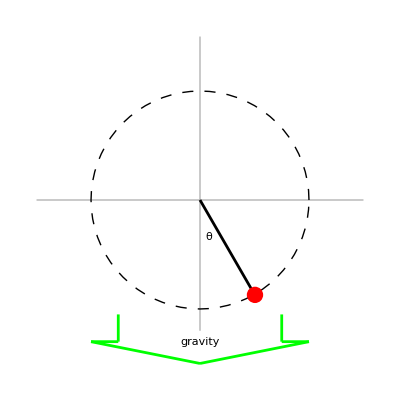

```mathematica
Show[Graphics[{
{GrayLevel[0.7],Line[{{-3,0},{3,0}}]},{GrayLevel[0.7],Line[{{0,-2.4},{0,3}}]},
{Dashing[{.02,.02}],Circle[{0,0},2]},
{AbsoluteThickness[2],Line[{{0,0},{2Sin[π/6],-2Cos[π/6]}}]},
{Red,Disk[{2Sin[π/6],-2Cos[π/6]},.15]},Text["θ",{.7Sin[π/14],-.7Cos[π/14]}],
Text["gravity",{0,-2.6}],
{Green,AbsoluteThickness[2],Line[{{-1.5,-2.1},{-1.5,-2.6}}]},
{Green,AbsoluteThickness[2],Line[{{-1.5,-2.6},{-2,-2.6}}]},
{Green,AbsoluteThickness[2],Line[{{-2,-2.6},{0,-3}}]},
{Green,AbsoluteThickness[2],Line[{{0,-3},{2,-2.6}}]},
{Green,AbsoluteThickness[2],Line[{{2,-2.6},{1.5,-2.6}}]},
{Green,AbsoluteThickness[2],Line[{{1.5,-2.6},{1.5,-2.1}}]}}],
PlotRange->All,
AspectRatio->Automatic]
```

Taking the system to have zero potential energy when it is at rest, the potential energy function becomes

```mathematica
U[θ]=m g a(1-cos θ)=m ω^2 a^2(1-cos θ)
```

where ω^2=g/a and a denotes "rod length." Assume initially that we have adopted units in which

```mathematica
m=g=a=1
```

Then

```mathematica
potentialenergy[θ_]:=1-Cos[θ]
```

which in the small angle approximation becomes

```mathematica
Series[potentialenergy[θ],{θ,0,2}]
```

θ^2/2+O[θ]^3

We construct superimposed plots of those two functions:

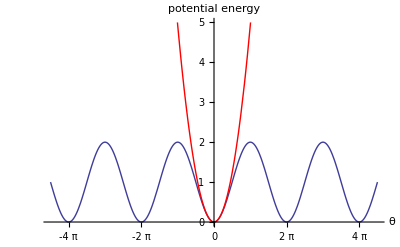

```mathematica
Plot[{potentialenergy[θ],θ^2/2},{θ,-9/2 π,9/2 π},
PlotStyle->{{},Red},
Ticks->{{-4π,-2π,0,2π,4π},Automatic},
AxesLabel->{"θ","potential energy"}, PlotRange->{0,5}]
```

The pendulum moves harmonically only in the small-angle regime where the red and blue curves are indistinguishable.

The equation of motion of a simple undamped pendulum reads (here we suspend our assumption that m = g = a = 1, which would have entailed ω^2=1)

```mathematica
θ''[t]==-ω^2 Sin[θ[t]]
```

(here  ω^2≡g/m) which by

```mathematica
Series[-ω^2 Sin[θ],{θ,0,6}]
```

-ω^2 θ+(ω^2 θ^3)/6-(ω^2 θ^5)/120+O[θ]^7

is seen to be a nonlinear 2nd-order ODE. We are therefore not surprised that, when asked to solve the equation (in which, for the illusrative purposes of this discussion, I will set ω==3), Mathematica responds cryptically/disappointingly and finally not at all:

```mathematica
θ[t]/.First[DSolve[{θ''[t]==-3^2 Sin[θ[t]],θ[0]==0,θ'[0]==3},θ[t],t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvfail: For some branches of the general solution, unable to solve the conditions.

First::first: {} has a length of zero and no first element.

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

θ[t]/.First[{}]

To simplify the question we are asking of Mathematica, we drop the initial conditions

```mathematica
DSolve[{θ''[t]==-3^2 Sin[θ[t]]},θ[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ[t]→-2 JacobiAmplitude[1/2 √((18+C[1]) (t+C[2])^2),36/(18+C[1])]},{θ[t]→2 JacobiAmplitude[1/2 √((18+C[1]) (t+C[2])^2),36/(18+C[1])]}}

```mathematica
?JacobiAmplitude
```

JacobiAmplitude[u,m] gives the amplitude am(u|m) for Jacobi elliptic functions.

We could follow the » to see what Mathematica can tell us about the properties of the unfamiliar functions to which the physics of simple pendula has unexpectedly led us. Or we might consult the mathematical handbooks  (see, e.g., J. Spanier & K. B. Oldham, An Atlas of Functions (1987), page 637). We will see how far we can go without making such an effort—trusting to Mathematica's knowledge of the subject. Noting that the solutions presented above differ only in sign, we write

```mathematica
θ[t_,C1_,C2_]:=2 JacobiAmplitude[1/2 √((18+C1) (t+C2)^2),36/(18+C1)]
```

and must now figure out how to impose the initial conditions

```mathematica
θ[0,C1,C2]=0
D[θ[0,C1,C2],t]=ω0
```

We begin by looking graphically for the (x,y)-values for which the condition

```mathematica
2 JacobiAmplitude[x,y]=0
```

is satisfied: this we do in two distinct ways, each of which will take the better part of a minute:

```mathematica
Manipulate[Plot[Re[2 JacobiAmplitude[x,y]],{x,-1,1}, PlotRange->{-2,2}, AxesLabel->{"x"}],{y,-4,4}]
```

```mathematica
Manipulate[Plot[Re[2 JacobiAmplitude[x,y]],{y,-6,6},PlotRange->{-2,2}, AxesLabel->{"y"}],{x,-6,6}]
```

COMPLAINT: Mathematica 5.2 a version of this figure with much higher resolution (PlotPoints→100) in much less time than Mathematica 6 manages to do.

It appears on this evidence to be most natural to set

```mathematica
x≡1/2 √((18+C1) C2^2)=0
```

which—if we are to prevent

```mathematica
y≡36/(18+C1)
```

from blowing up—requires that we set C2 = 0. We are left with

```mathematica
θ[t,C1,0]
```

2 JacobiAmplitude[1/2 √((18+C1) t^2),36/(18+C1)]

Diffrentiating with respect to t

```mathematica
D[2 JacobiAmplitude[1/2 √((18+C1) t^2),36/(18+C1)],t]
```

((18+C1) t JacobiDN[1/2 √((18+C1) t^2),36/(18+C1)])/(√((18+C1) t^2))

we are led, after a little simplification, to introduce the angular velocity function

```mathematica
ω[t_,C1_]:=√(18+C1)  JacobiDN[1/2 √((18+C1) t^2),36/(18+C1)]
```

Then

```mathematica
ω[0,C1]
```

√(18+C1)

which we use to obtain

```mathematica
Solve[√(18+C1)==ω0,C1]
```

{{C1→-18+ω0^2}}

So we have

```mathematica
θ[t,-18+ω0^2,0]
```

2 JacobiAmplitude[1/2 √(t^2 ω0^2),36/ω0^2]

and are led to introduce the following description of angular motion as a function of initial angular velocity:

```mathematica
θ[t_,ω0_]:=2 JacobiAmplitude[1/2 ω0 t,36/ω0^2]
```

```mathematica
θ[t,3]
θ[t,10/3]
θ[t,11/3]
```

2 JacobiAmplitude[(3 t)/2,4]

2 JacobiAmplitude[(5 t)/3,81/25]

2 JacobiAmplitude[(11 t)/6,324/121]

CURIOUS FACT: We had to struggle a bit to obtain this description of the pendular motion that conforms to our stated initial conditions. Mathematica 4, which was used to produce the first edition of this manual, led spontaneously and immediately to our final result, with no struggle at all. Mathematica 5 was—as Mathematica 6 now is—for all of its virtues, in some respects "too smart," or at least annoyingly fussy: it detects—and forces the user to identify and resolve—ambiguities that earlier versions of the software were content to ignore.

Using the result now in hand to construct the following figure [REMARK: I do not understand why Mathematica 6 takes much longer to produce a figure very much inferior to that produced by earlier versions of Mathematica]

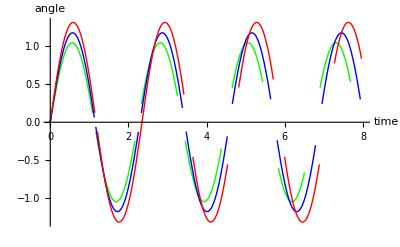

```mathematica
Plot[{θ[t,3],θ[t,10/3],θ[t,11/3]},{t,0,8},
PlotStyle->{{Green},{Blue},{Red}},
AxesLabel->{"time","angle"}]
```

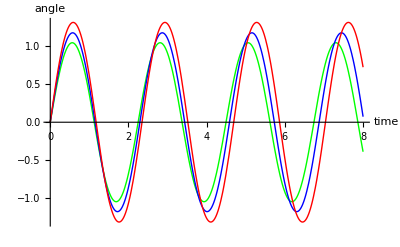

```mathematica
Plot[{Re[θ[t,3]],Re[θ[t,10/3]],Re[θ[t,11/3]]},{t,0,8},
PlotStyle->{{Green},{Blue},{Red}},
AxesLabel->{"time","angle"}]
```

it becomes vividly evident that increasing the initial angular velocity of (i.e., adding energy to) the pendulum serves not only to increase the amplitude of the oscillations but to increase also their period. Simple pendula have here been demonstrated to be (because the torque is not a linear function of angle) anharmonic.

If you give a pendulum a strong enough initial push it will go right over the top: rather than "oscillate" it will loop-the-loop or "librate". The conserved energy of our illustrative system can be described

```mathematica
PendulumEnergy[t_]:=1/2 θ'[t]^2+ω^2(1-Cos[θ[t]])
```

To check conservation, we examine

```mathematica
D[PendulumEnergy[t],t]//Simplify
```

θ'[t] (ω^2 Sin[θ[t]]+θ''[t])

which vanishes as a consequence of the equation of motion: ω^2 Sin[θ[t]]+θ''[t]= 0.

We plot isoenergetic curves on the (θ, θdot)-plane—here I write θdot  to denote angular velocity, and set ω = 3:

```mathematica
ContourPlot[1/2 θdot^2+3^2(1-Cos[θ]),
{θ,-3π,3π},{θdot,-3π,3π},
Contours->20,
FrameLabel->{"θ","θdot"},
PlotLabel->StyleForm["Isoenergetic  contours",
FontFamily->"Times-Bold",
FontSize->16]]
```

-Graphics-

The distinction between oscillation (closed curves) and libration (open curves) is now clearly evident.

Damped Pendulum

We look to the illustrative equation

```mathematica
θ''[t]==-θ'[t]-3^2 Sin[θ[t]]
```

which results from introducing a damping term into the equation studied in the preceding section. Mathematica thinks for awhile, then informs us that it is unable to supply an analytical solution

```mathematica
DSolve[{θ''[t]==-θ'[t]-3^2 Sin[θ[t]]},θ[t],t]//Timing
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{21.2667,DSolve[{θ''[t]==-9 Sin[θ[t]]-θ'[t]},θ[t],t]}

so we proceed numerically, taking our initial conditions to be identical to those adopted at the beginning of the preceding discussion:

```mathematica
NDSolve[{θ''[t]==-θ'[t]-3^2 Sin[θ[t]],θ[0]==0,θ'[0]==3},θ[t],{t,0,10}]
```

{{θ[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

Or better—as Wagon (on his p. 298) has taught us to do—we define:

```mathematica
dampedpendulum3000=θ[t]/.First[NDSolve[{θ''[t]==-θ'[t]-3^2 Sin[θ[t]],θ[0]==0,θ'[0]==3},θ[t],{t,0,10}]]
```

InterpolatingFunction[{{0.,10.}},<>][t]

The InterpolatingFunction is a bunch of data that now lives in Mathematica's memory. We use graphical means to extract that data:

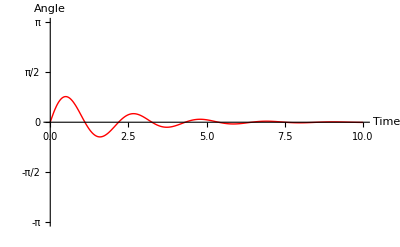

```mathematica
Plot[Evaluate[dampedpendulum3000],{t,0,10},
PlotStyle->RGBColor[1,0,0],
PlotRange->{-π,π},
Ticks->{Automatic,{-π,-1/2 π,0,1/2 π,π}},
AxesLabel->{Time, Angle}]
```

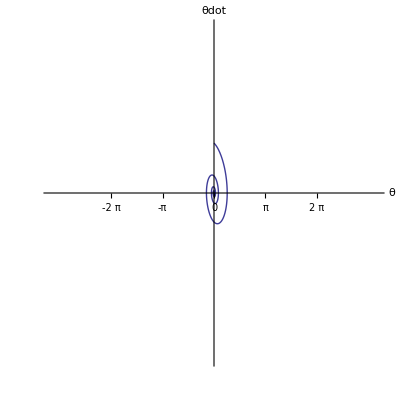

```mathematica
g1=ParametricPlot[Evaluate[{dampedpendulum3000,D[dampedpendulum3000,t]}],{t,0,10},
PlotRange->{{-10,10},{-10,10}},
PlotPoints->300,
Ticks->{{-2π,-π,0,π,2π},None},
AxesLabel->{θ,"θdot"}]
```

In the following series of figures we explore the effect of giving the damped pendulum progressively increased amounts of initial energy (increasingly higher initial velocities):

```mathematica
dampedpendulum4000=θ[t]/.First[NDSolve[{θ''[t]==-θ'[t]-3^2 Sin[θ[t]],θ[0]==0,θ'[0]==4},θ[t],{t,0,10}]]
```

InterpolatingFunction[{{0.,10.}},<>][t]

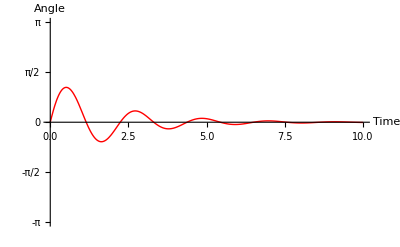

```mathematica
Plot[Evaluate[dampedpendulum4000],{t,0,10},
PlotStyle->RGBColor[1,0,0],
PlotRange->{-π,π},
Ticks->{Automatic,{-π,-1/2 π,0,1/2 π,π}},
AxesLabel->{Time, Angle}]
```

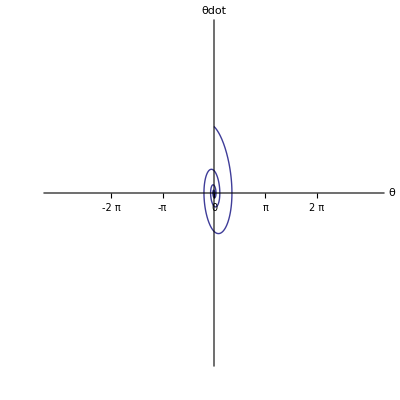

```mathematica
g2=ParametricPlot[Evaluate[{dampedpendulum4000,D[dampedpendulum4000,t]}],{t,0,10},
PlotRange->{{-10,10},{-10,10}},
PlotPoints->300,
Ticks->{{-2π,-π,0,π,2π},None},
AxesLabel->{θ,"θdot"}]
```

```mathematica
dampedpendulum5000=θ[t]/.First[NDSolve[{θ''[t]==-θ'[t]-3^2 Sin[θ[t]],θ[0]==0,θ'[0]==5},θ[t],{t,0,10}]]
```

InterpolatingFunction[{{0.,10.}},<>][t]

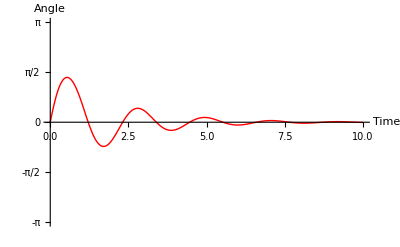

```mathematica
Plot[Evaluate[dampedpendulum5000],{t,0,10},
PlotStyle->RGBColor[1,0,0],
PlotRange->{-π,π},
Ticks->{Automatic,{-π,-1/2 π,0,1/2 π,π}},
AxesLabel->{Time, Angle}]
```

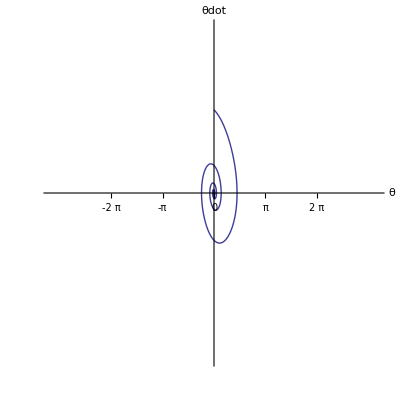

```mathematica
g3=ParametricPlot[Evaluate[{dampedpendulum5000,D[dampedpendulum5000,t]}],{t,0,10},
PlotRange->{{-10,10},{-10,10}},
PlotPoints->300,
Ticks->{{-2π,-π,0,π,2π},None},
AxesLabel->{θ,"θdot"}]
```

```mathematica
dampedpendulum6000=θ[t]/.First[NDSolve[{θ''[t]==-θ'[t]-3^2 Sin[θ[t]],θ[0]==0,θ'[0]==6},θ[t],{t,0,10}]]
```

InterpolatingFunction[{{0.,10.}},<>][t]

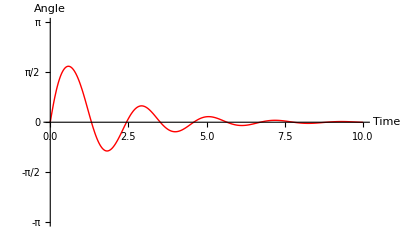

```mathematica
Plot[Evaluate[dampedpendulum6000],{t,0,10},
PlotStyle->RGBColor[1,0,0],
PlotRange->{-π,π},
Ticks->{Automatic,{-π,-1/2 π,0,1/2 π,π}},
AxesLabel->{Time, Angle}]
```

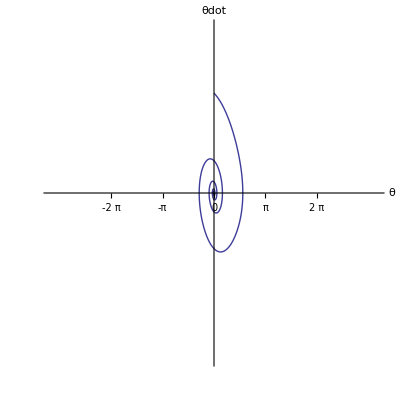

```mathematica
g4=ParametricPlot[Evaluate[{dampedpendulum6000,D[dampedpendulum6000,t]}],{t,0,10},
PlotRange->{{-10,10},{-10,10}},
PlotPoints->300,
Ticks->{{-2π,-π,0,π,2π},None},
AxesLabel->{θ,"θdot"}]
```

```mathematica
dampedpendulum7000=θ[t]/.First[NDSolve[{θ''[t]==-θ'[t]-3^2 Sin[θ[t]],θ[0]==0,θ'[0]==7},θ[t],{t,0,10}]]
```

InterpolatingFunction[{{0.,10.}},<>][t]

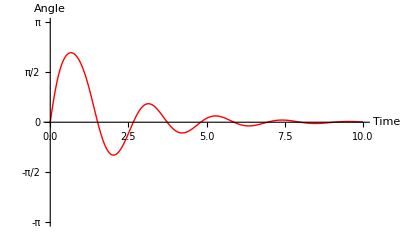

```mathematica
Plot[Evaluate[dampedpendulum7000],{t,0,10},
PlotStyle->RGBColor[1,0,0],
PlotRange->{-π,π},
Ticks->{Automatic,{-π,-1/2 π,0,1/2 π,π}},
AxesLabel->{Time, Angle}]
```

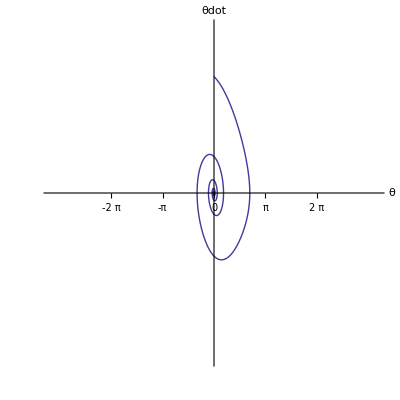

```mathematica
g5=ParametricPlot[Evaluate[{dampedpendulum7000,D[dampedpendulum7000,t]}],{t,0,10},
PlotRange->{{-10,10},{-10,10}},
PlotPoints->300,
Ticks->{{-2π,-π,0,π,2π},None},
AxesLabel->{θ,"θdot"}]
```

```mathematica
dampedpendulum8000=θ[t]/.First[NDSolve[{θ''[t]==-θ'[t]-3^2 Sin[θ[t]],θ[0]==0,θ'[0]==8},θ[t],{t,0,10}]]
```

InterpolatingFunction[{{0.,10.}},<>][t]

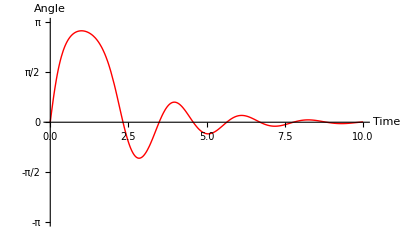

```mathematica
Plot[Evaluate[dampedpendulum8000],{t,0,10},
PlotStyle->RGBColor[1,0,0],
PlotRange->{-π,π},
Ticks->{Automatic,{-π,-1/2 π,0,1/2 π,π}},
AxesLabel->{Time, Angle}]
```

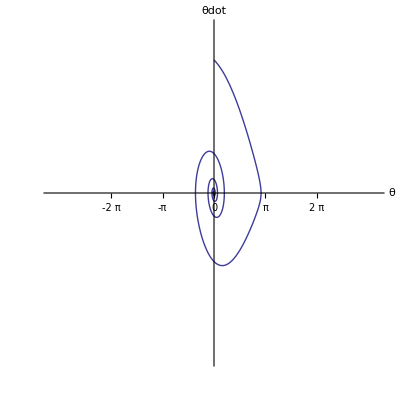

```mathematica
ParametricPlot[Evaluate[{dampedpendulum8000,D[dampedpendulum8000,t]}],{t,0,10},
PlotRange->{{-10,10},{-10,10}},
PlotPoints->300,
Ticks->{{-2π,-π,0,π,2π},None},
AxesLabel->{θ,"θdot"}]
```

```mathematica
dampedpendulum8121=θ[t]/.First[NDSolve[{θ''[t]==-θ'[t]-3^2 Sin[θ[t]],θ[0]==0,θ'[0]==8.121},θ[t],{t,0,15}]]
```

InterpolatingFunction[{{0.,15.}},<>][t]

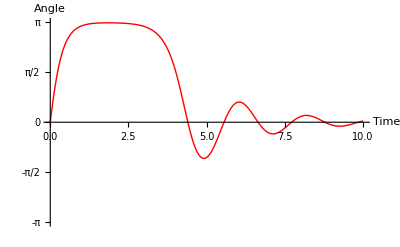

```mathematica
Plot[Evaluate[dampedpendulum8121],{t,0,10},
PlotStyle->RGBColor[1,0,0],
PlotRange->{-π,π},
Ticks->{Automatic,{-π,-1/2 π,0,1/2 π,π}},
AxesLabel->{Time, Angle}]
```

Note that the pendulum hesitates as it approaches the top of its arc. This shows up in the following figure as a kink (why?).

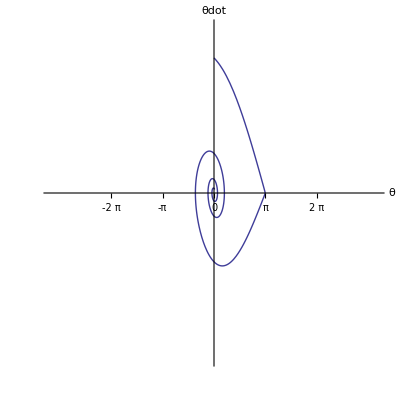

```mathematica
g6=ParametricPlot[Evaluate[{dampedpendulum8121,D[dampedpendulum8121,t]}],{t,0,10},
PlotRange->{{-10,10},{-10,10}},
PlotPoints->300,
Ticks->{{-2π,-π,0,π,2π},None},
AxesLabel->{θ,"θdot"}]
```

```mathematica
dampedpendulum8122=θ[t]/.First[NDSolve[{θ''[t]==-θ'[t]-3^2 Sin[θ[t]],θ[0]==0,θ'[0]==8.122},θ[t],{t,0,15}]]
```

InterpolatingFunction[{{0.,15.}},<>][t]

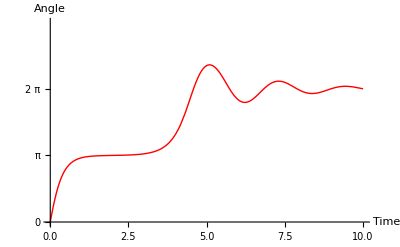

```mathematica
Plot[Evaluate[dampedpendulum8122],{t,0,10},
PlotStyle->RGBColor[1,0,0],
PlotRange->{-0,3π},
Ticks->{Automatic,{0,π,2π}},
AxesLabel->{Time, Angle}]
```

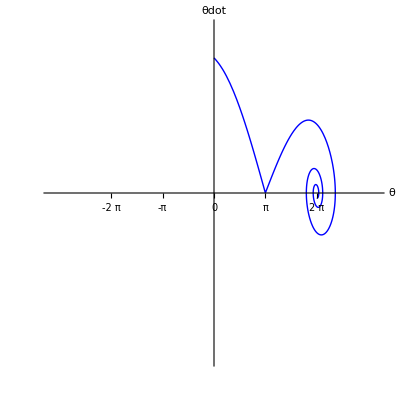

```mathematica
g7=ParametricPlot[Evaluate[{dampedpendulum8122,D[dampedpendulum8122,t]}],{t,0,10},
PlotRange->{{-10,10},{-10,10}},
PlotStyle->RGBColor[0,0,1],
PlotPoints->300,
Ticks->{{-2π,-π,0,π,2π},None},
AxesLabel->{θ,"θdot"}]
```

```mathematica
dampedpendulum9000=θ[t]/.First[NDSolve[{θ''[t]==-θ'[t]-3^2 Sin[θ[t]],θ[0]==0,θ'[0]==9},θ[t],{t,0,10}]]
```

InterpolatingFunction[{{0.,10.}},<>][t]

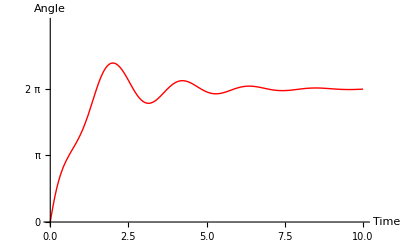

```mathematica
Plot[Evaluate[dampedpendulum9000],{t,0,10},
PlotStyle->RGBColor[1,0,0],
PlotRange->{-0,3π},
Ticks->{Automatic,{0,π,2π}},
AxesLabel->{Time, Angle},
PlotRange->All]
```

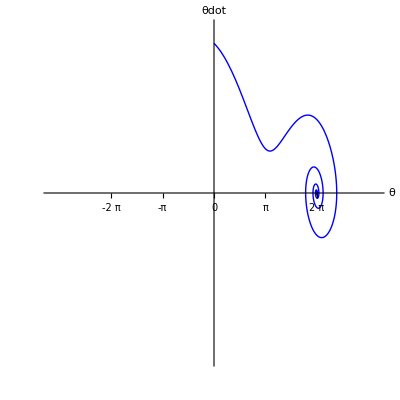

```mathematica
g8=ParametricPlot[Evaluate[{dampedpendulum9000,D[dampedpendulum9000,t]}],{t,0,10},
PlotRange->{{-10,10},{-10,10}},
PlotStyle->RGBColor[0,0,1],
PlotPoints->300,
Ticks->{{-2π,-π,0,π,2π},None},
AxesLabel->{θ,"θdot"}]
```

```mathematica
dampedpendulum10000=θ[t]/.First[NDSolve[{θ''[t]==-θ'[t]-3^2 Sin[θ[t]],θ[0]==0,θ'[0]==10},θ[t],{t,0,10}]]
```

InterpolatingFunction[{{0.,10.}},<>][t]

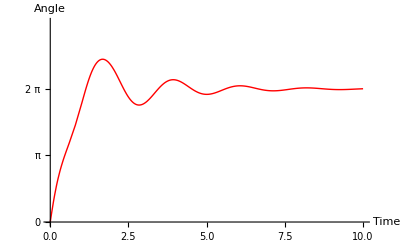

```mathematica
Plot[Evaluate[dampedpendulum10000],{t,0,10},
PlotStyle->RGBColor[1,0,0],
PlotRange->{-0,3π},
Ticks->{Automatic,{0,π,2π}},
AxesLabel->{Time, Angle},
PlotRange->All]
```

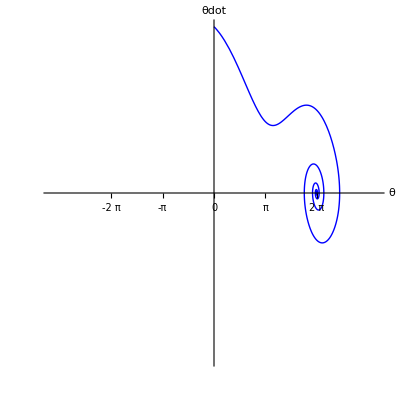

```mathematica
g9=ParametricPlot[Evaluate[{dampedpendulum10000,D[dampedpendulum10000,t]}],{t,0,10},
PlotRange->{{-10,10},{-10,10}},
PlotStyle->RGBColor[0,0,1],
PlotPoints->300,
Ticks->{{-2π,-π,0,π,2π},None},
AxesLabel->{θ,"θdot"}]
```

Superimposing all the parametric plots, we obtain

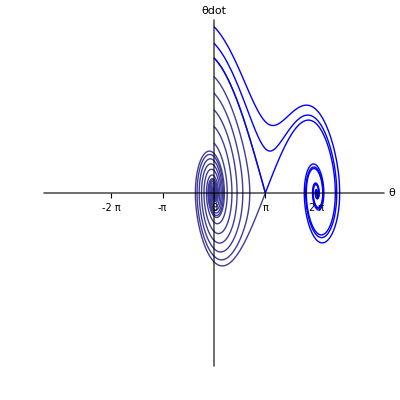

```mathematica
Show[{g1,g2,g3,g4,g5,g6,g7,g8,g9},
Ticks->{{-2π,-π,0,π,2π},None},
AxesLabel->{θ,"θdot"}]
```

A little quick experimentation enables us to discovery of the (approximate) least value of initial velocity that is sufficient to cause the pendulum to (barely) go twice over the top:

```mathematica
twiceover1=θ[t]/.First[NDSolve[{θ''[t]==-θ'[t]-3^2 Sin[θ[t]],θ[0]==0,θ'[0]==13.89},θ[t],{t,0,10}]]
```

InterpolatingFunction[{{0.,10.}},<>][t]

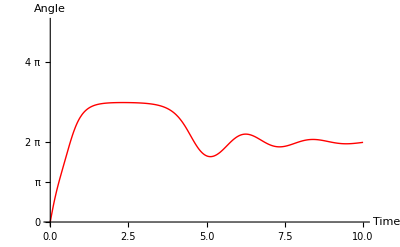

```mathematica
Plot[Evaluate[twiceover1],{t,0,10},
PlotStyle->RGBColor[1,0,0],
PlotRange->{-0,5π},
Ticks->{Automatic,{0,π,2π,4π}},
AxesLabel->{Time, Angle},
PlotRange->All]
```

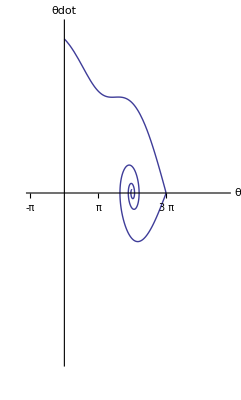

```mathematica
g21=ParametricPlot[Evaluate[{twiceover1,D[twiceover1,t]}],{t,0,10},
PlotRange->{{-π,15},{-15,15}},
PlotPoints->300,
Ticks->{{-π,0,π,2π,3π,4π},None},
AxesLabel->{θ,"θdot"}]
```

```mathematica
twiceover2=θ[t]/.First[NDSolve[{θ''[t]==-θ'[t]-3^2 Sin[θ[t]],θ[0]==0,θ'[0]==13.90},θ[t],{t,0,10}]]
```

InterpolatingFunction[{{0.,10.}},<>][t]

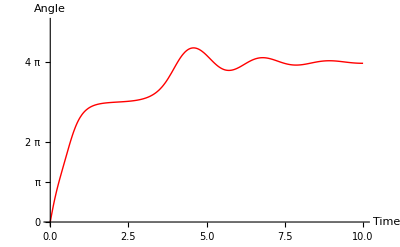

```mathematica
Plot[Evaluate[twiceover2],{t,0,10},
PlotStyle->RGBColor[1,0,0],
PlotRange->{-0,5π},
Ticks->{Automatic,{0,π,2π,4π}},
AxesLabel->{Time, Angle},
PlotRange->All]
```

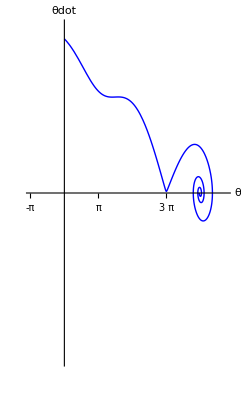

```mathematica
g22=ParametricPlot[Evaluate[{twiceover2,D[twiceover2,t]}],{t,0,10},
PlotRange->{{-π,15},{-15,15}},
PlotStyle->RGBColor[0,0,1],
PlotPoints->300,
Ticks->{{-π,0,π,2π,3π,4π},None},
AxesLabel->{θ,"θdot"}]
```

In preparation for the next superimposition of figures we prepare variants of a couple of previous figures (the only adjustment is that we have extended the θ-range), which we paint gray:

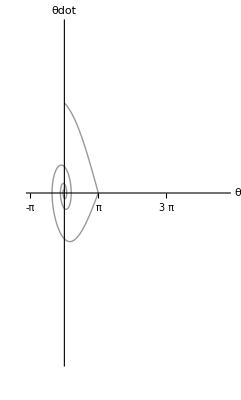

```mathematica
G1=ParametricPlot[Evaluate[{dampedpendulum8121,D[dampedpendulum8121,t]}],{t,0,10},
PlotRange->{{-π,15},{-15,15}},
PlotStyle->GrayLevel[.6],
PlotPoints->300,
Ticks->{{-π,0,π,2π,3π,4π},None},
AxesLabel->{θ,"θdot"}]
```

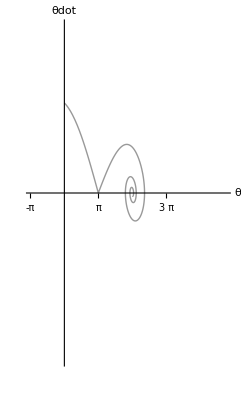

```mathematica
G2=ParametricPlot[Evaluate[{dampedpendulum8122,D[dampedpendulum8122,t]}],{t,0,10},
PlotRange->{{-π,15},{-15,15}},
PlotStyle->GrayLevel[.6],
PlotPoints->300,
Ticks->{{-π,0,π,2π,3π,4π},None},
AxesLabel->{θ,"θdot"}]
```

Now the final superpositon:

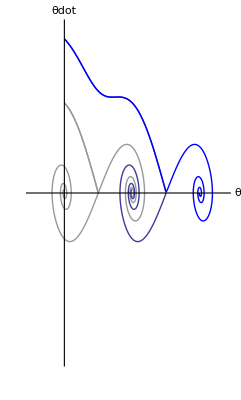

```mathematica
Show[{G1,G2,g21,g22},Ticks->None]
```

Animation provides still another way to display the motion of a damped pendulum.

```mathematica
Manipulate[Show[Graphics[{
{GrayLevel[0.7],Line[{{-3,0},{3,0}}]},{GrayLevel[0.7],Line[{{0,-2.4},{0,3}}]},
{Dashing[{.02,.02}],Circle[{0,0},2]},
{AbsoluteThickness[2],Line[{{0,0},{2Sin[ dampedpendulum8122 /.t->tt],-2Cos[  dampedpendulum8122]/.t->tt }}]},
{Red,Disk[{2Sin[dampedpendulum8122/.t->tt],-2Cos[ dampedpendulum8122/.t->tt]},.15]},
Text["gravity",{0,-2.6}],
{Green,AbsoluteThickness[2],Line[{{-1.5,-2.1},{-1.5,-2.6}}]},
{Green,AbsoluteThickness[2],Line[{{-1.5,-2.6},{-2,-2.6}}]},
{Green,AbsoluteThickness[2],Line[{{-2,-2.6},{0,-3}}]},
{Green,AbsoluteThickness[2],Line[{{0,-3},{2,-2.6}}]},
{Green,AbsoluteThickness[2],Line[{{2,-2.6},{1.5,-2.6}}]},
{Green,AbsoluteThickness[2],Line[{{1.5,-2.6},{1.5,-2.1}}]}}],
PlotRange->All,
AspectRatio->Automatic],{tt,0,10,0.05}]
```

INSTRUCTION: Run as a movie.

This is an amusing creation, but raises a philosophical point:

It is gratifying to find that our animations "reproduce the real world," but to the extent that they do so they teach us little more than we would learn by simply looking at the world itself. Previous modes of graphical display—though more "diagramatic," and though they may require some interpretive practice—speak more clearly/informatively to what is going on, teach us how to look at the real world. This much is, in any event clear: When you have solved a differential equation your work is typically only half done; you have yet to devise the best way, in the particular instance, to make your result intelligible. Strings of data—produced maybe this way

```mathematica
Table[dampedpendulum8122/(2π)/.t->k,{k,0,10,.5}]//TableForm
```

-8.40713×10^-22
0.3996
0.482879
0.497354
0.500507
0.503497
0.512747
0.54538
0.657812
0.947084
1.17548
1.09197
0.920516
0.927996
1.0341
1.04922
0.987267
0.968252
1.00298
1.01968
1.00105

+

may be all you need in some few cases, but graphical display is often your most powerful resource.  It is a resource which Mathematica permits you to manage with unprecedented power and efficiency.

### Ballistics

Consider the motion of a thrown mass point; immediately

```mathematica
{x[t],y[t]}/.First[DSolve[{x''[t]==0,y''[t]==-g,x[0]==0,y[0]==0,x'[0]==v Cos[θ],y'[0]==v Sin[θ]},{x[t],y[t]}, t]]
```

{t v Cos[θ],1/2 (-g t^2+2 t v Sin[θ])}

This, of course, is physics learned in the second week of an introductory course.  If—after defining

```mathematica
x[t_,v_,θ_,g_]:=t v Cos[θ]
y[t_,v_,θ_,g_]:=1/2 (-g t^2+2 t v Sin[θ])
```

+

—we make a table of figures (various launch angles, constant launch speed: I use ; to surpress immediate display of the figures)

```mathematica
undampedflight=Table[ParametricPlot[{x[t,8,k/20 π/2,4],y[t,8,k/20 π/2,4]},{t,0,4},PlotRange->{{0,17},{0,8.5}},
Ticks->None,
AspectRatio->Automatic],{k,0,19}];
```

and superimpose those figures

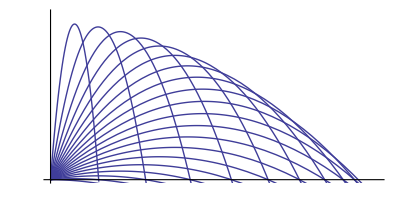

```mathematica
Show[undampedflight]
```

we obtain an image which has been engraved in physics books since the mid-1600s.

But the following steps culminate in a variant of that same familiar figure which contains an element of surprise. First we draw the arcs traced by particles which are launched (all with the same speed) in various directions

```mathematica
arcimages=Table[ParametricPlot[{x[t,8,k(2π)/30,4],y[t,8,k(2π)/30,4]},{t,0,4},PlotRange->{{-35,35},{-70,10}},
Ticks->None,
AspectRatio->Automatic],{k,0,29}];
```

Next we construct a representation of where that population of particles resides at time t = 4:

```mathematica
flashtable=Table[Point[{x[4,8,k(2π)/30,4],y[4,8,k(2π)/30,4]}],{k,0,29}];
```

```mathematica
flashimages=Graphics[{PointSize[0.02],RGBColor[1,0,0],flashtable}];
```

Finally, we superimpose those figures:

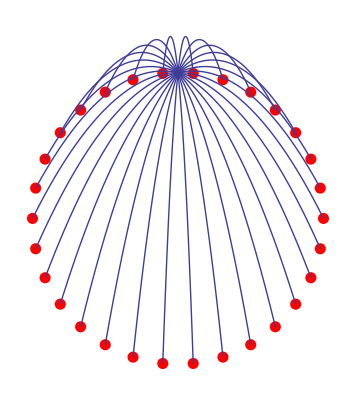

```mathematica
Show[{flashimages,arcimages},
PlotRange->All,
AspectRatio->Automatic]
```

The circle is the surprise…though when you think about it, such circles are seen every 4th of July, and become quite unsurprising when you consider how the particle motion would appear to an observer falling from the explosion point.

We are in position now to do also things not commonly done in an introductory course. For example: let us suppose a thrown projectile experiences a drag force of the form

```mathematica
drag vector=-(drag coefficient)(velocity vector)
```

We ask Mathematica to solve

```mathematica
{X[t],Y[t]}/.First[DSolve[{X''[t]==-b X'[t],Y''[t]==-b Y'[t]-g,X[0]==0,Y[0]==0,X'[0]==v Cos[θ],Y'[0]==v Sin[θ]},{X[t],Y[t]}, t]]
```

{(ⅇ^(-b t) (-1+ⅇ^(b t)) v Cos[θ])/b,-(ⅇ^(-b t) (g-ⅇ^(b t) g+b ⅇ^(b t) g t+b v Sin[θ]-b ⅇ^(b t) v Sin[θ]))/b^2}

and on this basis define the functions

```mathematica
X[t_,v_,θ_,b_]:=(ⅇ^(-b t) (-1+ⅇ^(b t)) v Cos[θ])/b
Y[t_,v_,θ_,g_,b_]:=-1/b^2(ⅇ^(-b t) (g-ⅇ^(b t) g+b ⅇ^(b t) g t+b v Sin[θ]-b ⅇ^(b t) v Sin[θ]))
```

which we feed into the following graphic:

```mathematica
dampedflight=Table[ParametricPlot[{X[t,8,k/20 π/2,3/10],Y[t,8,k/20 π/2,4,3/10]},{t,0,4},PlotRange->{{0,17},{0,8.5}},
Ticks->None,
AspectRatio->Automatic,
PlotStyle->RGBColor[0,0,1]],{k,0,19}];
```

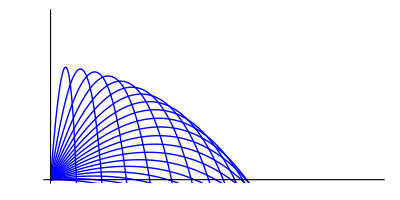

```mathematica
Show[dampedflight]
```

We are in position now to provide a direct comparison of damped with undamped ballistic trajectories:

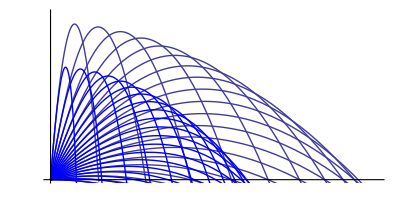

```mathematica
Show[undampedflight,dampedflight]
```

### Planetary Motion

So well known is this problem that, without physical preamble, we proceed

```mathematica
Clear[x,y,a,b]
```

```mathematica
DSolve[{x''[t]==-x[t]/((x[t]^2+y[t]^2)^(3/2)),y''[t]==-y[t]/((x[t]^2+y[t]^2)^(3/2))},{x[t],y[t]},t]
```

DSolve[{x''[t]==-x[t]/((x[t]^2+y[t]^2)^(3/2)),y''[t]==-y[t]/((x[t]^2+y[t]^2)^(3/2))},{x[t],y[t]},t]

and find that Mathematica is unwilling to provide a general solution in analytical closed form.  So we proceed numerically (which obliges us to specify some experimental initial conditions):

```mathematica
orbit1=NDSolve[{x''[t]==-x[t]/((x[t]^2+y[t]^2)^(3/2)),y''[t]==-y[t]/((x[t]^2+y[t]^2)^(3/2)),x[0]==1,y[0]==0,x'[0]==0,y'[0]==.5},{x[t],y[t]},{t,0,3}]
```

{{x[t]→InterpolatingFunction[{{0.,3.}},<>][t],y[t]→InterpolatingFunction[{{0.,3.}},<>][t]}}

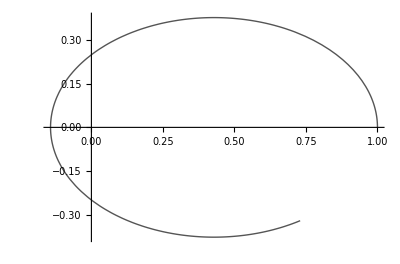

```mathematica
firstorbit=ParametricPlot[Evaluate[{x[t],y[t]}/.orbit1],{t,0,2},
PlotRange->All,
 AspectRatio->Automatic,
PlotStyle->RGBColor[1/3,1/3,1/3]]
```

We increase slightly the y-component of initial velocity:

```mathematica
orbit2=NDSolve[{x''[t]==-x[t]/((x[t]^2+y[t]^2)^(3/2)),y''[t]==-y[t]/((x[t]^2+y[t]^2)^(3/2)),x[0]==1,y[0]==0,x'[0]==0,y'[0]==.6},{x[t],y[t]},{t,0,3}]
```

{{x[t]→InterpolatingFunction[{{0.,3.}},<>][t],y[t]→InterpolatingFunction[{{0.,3.}},<>][t]}}

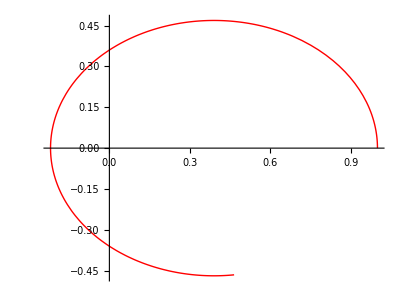

```mathematica
secondorbit=ParametricPlot[Evaluate[{x[t],y[t]}/.orbit2],{t,0,2},
PlotRange->All,
 AspectRatio->Automatic,
PlotStyle->Red]
```

and now we make a similar downward adjustment:

```mathematica
orbit3=NDSolve[{x''[t]==-x[t]/((x[t]^2+y[t]^2)^(3/2)),y''[t]==-y[t]/((x[t]^2+y[t]^2)^(3/2)),x[0]==1,y[0]==0,x'[0]==0,y'[0]==.4},{x[t],y[t]},{t,0,3}]
```

{{x[t]→InterpolatingFunction[{{0.,3.}},<>][t],y[t]→InterpolatingFunction[{{0.,3.}},<>][t]}}

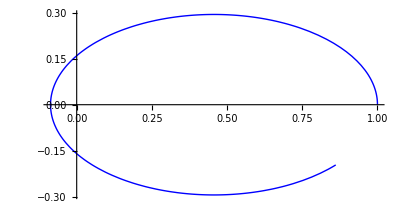

```mathematica
thirdorbit=ParametricPlot[Evaluate[{x[t],y[t]}/.orbit3],{t,0,2},
PlotRange->All,
 AspectRatio->Automatic,
PlotStyle->Blue]
```

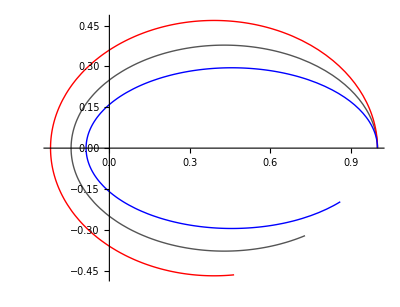

```mathematica
Show[firstorbit, secondorbit,thirdorbit]
```

One could write a book about this system (as Newton was the first to do, and NASA more recently has), but I will make only one further observation—illustrative of how easy it is to go exploring with the bright assistance of Mathematica. Let us modify—slightly—the force law:

```mathematica
superperturbedorbit=NDSolve[{x''[t]==-x[t]/((x[t]^2+y[t]^2)^1.51),y''[t]==-y[t]/((x[t]^2+y[t]^2)^1.51),x[0]==1,y[0]==0,x'[0]==0,y'[0]==.4},{x[t],y[t]},{t,0,10}]
```

{{x[t]→InterpolatingFunction[{{0.,10.}},<>][t],y[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

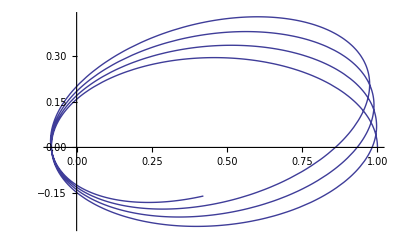

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.superperturbedorbit],{t,0,9},
PlotRange->All,
 AspectRatio->Automatic]
```

Compare that non-reentrant orbit with the following one:

```mathematica
subperturbedorbit=NDSolve[{x''[t]==-x[t]/((x[t]^2+y[t]^2)^1.49),y''[t]==-y[t]/((x[t]^2+y[t]^2)^1.49),x[0]==1,y[0]==0,x'[0]==0,y'[0]==.4},{x[t],y[t]},{t,0,10}]
```

{{x[t]→InterpolatingFunction[{{0.,10.}},<>][t],y[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

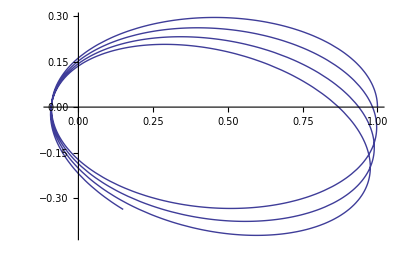

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.subperturbedorbit],{t,0,9},
PlotRange->All,
 AspectRatio->Automatic]
```

The precession is prograde in the former case, retrograde in the latter. The following experiment

```mathematica
barelysuperperturbedorbit=NDSolve[{x''[t]==-x[t]/((x[t]^2+y[t]^2)^1.5015),y''[t]==-y[t]/((x[t]^2+y[t]^2)^1.5015),x[0]==1,y[0]==0,x'[0]==0,y'[0]==.4},{x[t],y[t]},{t,0,15}]
```

{{x[t]→InterpolatingFunction[{{0.,15.}},<>][t],y[t]→InterpolatingFunction[{{0.,15.}},<>][t]}}

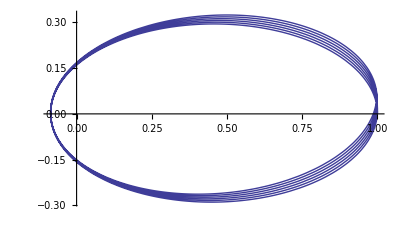

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.barelysuperperturbedorbit],{t,0,15},
PlotRange->All,
 AspectRatio->Automatic]
```

suggests that panetary data—since it extends back for millennia, and is taken with instruments of very high accuracy—can be used to establish that Newton's 2nd-power law is very accurately a 2nd-power law, else orbits might be expected to precess enough to come into conflict with observational data.

REMARK: Planetary evidence does not preclude the possibility that Newton's 2nd-power law stands in need of adjustment at distances much smaller/larger than those characteristic of the solar system. In recent years physicists have had reason to consider both possibilities, and at present neither has been altogether excluded.

### Initial Conditions Replaced by Endpoint Conditions

We are in the habit of specifying orbits by stipulating initial conditions, but in advanced mechanics one develops (in connection with the way certain "variational principles" are phrased) an interest in orbits/trajectories that conform to stipulated endpoint conditions; indeed, a right fielder has something resembling endpoint conditions in mind when he throws the ball, as does the quarterback when he throws a pass. Here I want only to point out that Mathematica takes endpoint conditions in easy stride.

Look, by way of illustration, to the familiar harmonic oscillator:

```mathematica
DSolve[{x''[t]==-ω^2 x[t],x[0]==a, x[T]==b},x[t],t]
```

{{x[t]→a Cos[t ω]-a Cot[T ω] Sin[t ω]+b Csc[T ω] Sin[t ω]}}

Here the side conditions have clearly the nature of endpoint conditions.

We resort once again to graphical techniques to display what we have accomplished: we hold fixed the values of the parameters (T, a, b) that serve to locate the specified endpoints while incrementing the sole remaining parameter (ω):

```mathematica
endpointpositions={Point[{0,.5}],Point[{7/4,-1}]};
```

```mathematica
endpointimages=Graphics[{PointSize[0.02],Red,endpointpositions}];
```

```mathematica
x[t_,T_,a_,b_,ω_]:=a Cos[t ω]+(-a Cot[T ω]+b Csc[T ω]) Sin[t ω]
```

```mathematica
connectingorbits=Plot[{
x[t,7/4,.5,-1,2π],
x[t,7/4,.5,-1,2π+.1],
x[t,7/4,.5,-1,2π+.2],
x[t,7/4,.5,-1,2π+.3],
x[t,7/4,.5,-1,2π+.4]},{t,0,7/4},PlotRange->{{-.2,2},{-2,2}},
Ticks->{{1.75},{.5}},AxesLabel->{time,displacement}];
```

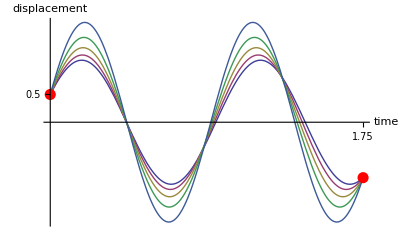

```mathematica
Show[{connectingorbits,endpointimages},
PlotRange->All]
```

### An Unexplored Resource

I have only just become aware of the existence of a resource which seems to be new in Mathematica 6, and which relates in what appears to be a very powerful to the graphic display of the solution of ODEs. It resides in the EquationTrekker package. To read about it, search for EquationTrekker/tutorial/EquationTrekker.